```mathematica
x=0
Z=2
```

0

2

```mathematica
{kcd@@#,kes@@#,kff@@#}^-1&@{10^3,6 10^1}//N
```

{1/(kcd(1000.,60.)),1/(kes(1000.,60.)),1/(kff(1000.,60.))}

Gotten from ....

```mathematica
kes[ρ_,T_] = 0.2 (1+x)
kff[ρ_,T_]= 41 ρ/((T/10^6)^(7/2))
krad[ρ_,T_]= (kes[ρ,T]^-1+ kff[ρ,T]^-1 )^-1
kcd[ρ_,T_]= (3.23 10^4 Z^2((T/10^6)^(1/2))/ρ)/(213 (ρ/10^6)^1/(μe (T/10^8)^(3/2)))/.μe-> 2
ktot[ρ_,T_]=(kcd[ρ,T]^-1+krad[ρ,T]^-1)^-1
```

0.2

(41000000000000000000000 ρ)/T^(7/2)

1/(T^(7/2)/(41000000000000000000000 ρ)+5.)

(1.21315×10^-6 T^2)/ρ^2

1/(5.+T^(7/2)/(41000000000000000000000 ρ)+(824303. ρ^2)/T^2)

Gotten from IOP-516819- “Updated Electron-Conduction Opacitites The Impact” : Cassisi Potekhin Pietrinkferni Catelan Salaris 2007

```mathematica
Quantity["hbar"]/(Quantity["Erg"] Quantity["s"])
```

1.054572×10^-27

```mathematica
Zi=2; A= 4;
(*TF[ρ_]:=5.93 10^9(√(1+(xr)^2) - 1)/.xr-> 0.01009(ρ Zi / A)^(1/3) (*TF in Kelvin, ρ in g/cm^3*) (*Is relativistic, but looks like holds for nonrel*)*)
ni[ρ_]:=ρ/(A (Quantity[1,"ProtonMass"]/Quantity["gram"]//UnitConvert))
ne[ρ_]:=ni[ρ]/2


me=(Quantity["ElectronMass"]/Quantity["gram"]//UnitConvert); ee =(√(Quantity["ElementaryCharge"]^2/(4π Quantity["ElectricConstant"])))/(√((Quantity["g"] Quantity["cm"]^3)/Quantity["s"]^2))//UnitConvert;α=ee^2/(4π);
hbar=Quantity["hbar"]/(Quantity["Erg"] Quantity["s"]); c = Quantity["SpeedOfLight"]/(Quantity["cm"]/Quantity["s"]);kB=Quantity["BoltzmannConstant"]/(Quantity["Erg"]/Quantity["Kelvin"]);σ=Quantity["StefanBoltzmannConstant"]/(Quantity["g"] Quantity["s"]^-3 Quantity["Kelvins"]^-4);



SetOpacities[ρ_,T_]:=Module[{a,χkinetic,ν,(*νei,νee,*)xr,pF,vF,βr,γr,y,Ir},
TF:=5.93 10^9(√(1+(xr)^2) - 1); (*TF in Kelvin, ρ in g/cm^3*) (*Is relativistic, but looks like holds for nonrel*)
xr= 0.01009(ρ Zi / A)^(1/3);
pF=me c  xr; γr=√(1+xr^2);vF=pF/(me γr);βr=vF/c;y=571.6/(T/10^6)βr^(1/2)xr;
a:= Piecewise[{{3/2,T≥ TF},{π^2/3,T<TF}}];
χkinetic:= (a ne[ρ] kB^2 T)/(me ν);
Λei:= Log[rmax/rmin]/.{rmax-> √((kB T)/(4π (ne[ρ] + Zi^2 ni[ρ])ee^2)),rmin-> Max[√((2π hbar^2)/(me kB T)),(Zi ee^2)/(kB T)]};
Λee:= Log[rmax/rmin]/.{rmax-> √((kB T)/(4π ne[ρ] ee^2)),rmin-> Max[√((2π hbar^2)/(me kB T)),ee^2/(kB T)]}; (*Same as above, but adjusted for electorn-electron by me*)

νei:= 4/3 √((2π)/me)(Zi^2 ee^4)/(kB T)^(3/2)ni[ρ] Λei;
νee:= 8/3 √(π/me)ee^4/(kB T)^(3/2)ne[ρ] Λee;
Ir=1/βr(10/63-(8/315)/(1+0.0435 y)) Log[1+128.56/(37.1y+10.83 y^2+y^3)]+βr^3(2.404/cB+ (cC-2.404/cB)/(1+0.1 βr y)) Log[1+cB/(cA βr y + (βr y)^2)] + βr/(1+cD)(cC + (18.52 βr^2 cD)/cB)Log[1+cB/(cA y + 10.83 (βr y)^2 +(βr y)^(8/3))]//. {cA->12.2 + 25.2 βr^3 ,cB->cA Exp[(0.123636 + 0.016234 βr^2)/cC] ,cC->8/105+0.05714 βr^4 ,cD->0.1558 y^(1-0.75 βr) };
Print[βr];

νeeDegen= ((me c^2)/hbar (6 α^(3/2))/π^(5/2)xr y √βr Ir)(1+t^2)/(1+t+b t^2 √(T/TF))/.{t-> 25 T/TF,b-> 0.434};
ν:=νei+ νeeDegen (*Only exactly right for completely degenrate electrons!*);
kcd:=(16 σ T^3)/(3 ρ χkinetic);

ktot:= (krad[ρ,T]^-1+ kcd[ρ,T]^-1)^-1;
]
SetOpacities[10^3,1];SetOpacities[10^7,10 TF]
T== 10 Tf== 10 TF
νee
νeeDegen
kcd
```

0.0798288

0.865186

T==10 Tf==5.89569×10^10

-2.33815×10^18

3.96861×10^-10

-0.473525

```mathematica
Evaluate@(SetOpacities[ρ,10^6];Log10@kcd)/.ρ-> 10^3
```

2.6776+1.3644 ⅈ

## Plot Section

```mathematica
TimmesData={{1009,6448231},
{3178,11794467},
{16030,29176619},
{50499,57841262},
{278233,148962490},
{1045722,346904386},
{2182053,450657034},
{6110740,745379806},
{7508264,775997174},
{23652659,1363375184},
{95682620,2813848425}}
```

(1009 | 6448231
3178 | 11794467
16030 | 29176619
50499 | 57841262
278233 | 148962490
1045722 | 346904386
2182053 | 450657034
6110740 | 745379806
7508264 | 775997174
23652659 | 1363375184
95682620 | 2813848425)

{{T→406030.}}

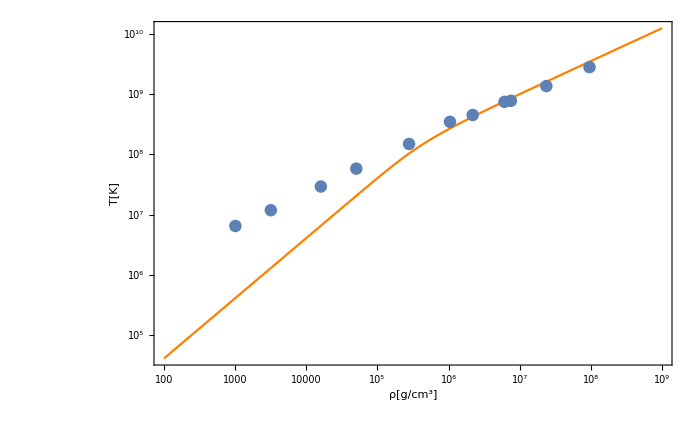

```mathematica
Tstar[ρ_?NumericQ]:=NSolve[{kcd[ρ,T]^-1==krad[ρ,T]^-1,T>0},T]
Tstar[10^3]
Show[
LogLogPlot[T/.Tstar[ρ],{ρ,10^2,10^9},ImageSize->700,GridLines->Automatic,Frame-> True,FrameStyle->Directive[FontSize-> 20],PlotStyle->Orange,FrameLabel->{"ρ[g/cm^3]","T[K]"}]
,ListLogLogPlot[TimmesData]
]
```

For all cases, for U kinetic enrgy density per volume, U=3/2 P, however what P is is strongly dependent on whether electrons are degenerate, etc.
Timmes uses  E=U/ρ

```mathematica
c= 3 10^10; MH = Quantity["AtomicMassUnit"]/Quantity["g"](*really hydrogen mass but whatever*);μe=2 ;k=(Quantity["BoltzmannConstant"]/(Quantity["g m^2"]/Quantity["s^2"]/Quantity["Kelvin"]))//UnitConvert//Simplify

ENRnonD[ρ_,T_]:= 3/2(1/μe ρ/MH k T)/ρ
ENRweakD[ρ_,T_]:= 3/2
ENRstrongD[ρ_,T_]:= 3/2(0.990647 10^13)1/ρ (ρ/(μe MH))^(5/3) (*In dynes/gram*)
ENRintD[ρ_,T_]:= 3/2
WT[ρ_,T_]:= √((c ENRnonD[ρ,T])/(ktot[ρ,T]S3alpha[ρ,T]))
MT[ρ_,T_]:= 4/3 π WT[ρ,T]^3 ρ
S3alpha[ρ_,T_]=5.1 10^8 ρ^2(1/(T/10^9))^3 E^(-4.4027/(T/10^9))
```

1.38065×10^-20

(5.1×10^35 ρ^2 ⅇ^(-4.4027×10^9/T))/T^3

2.79791×10^18

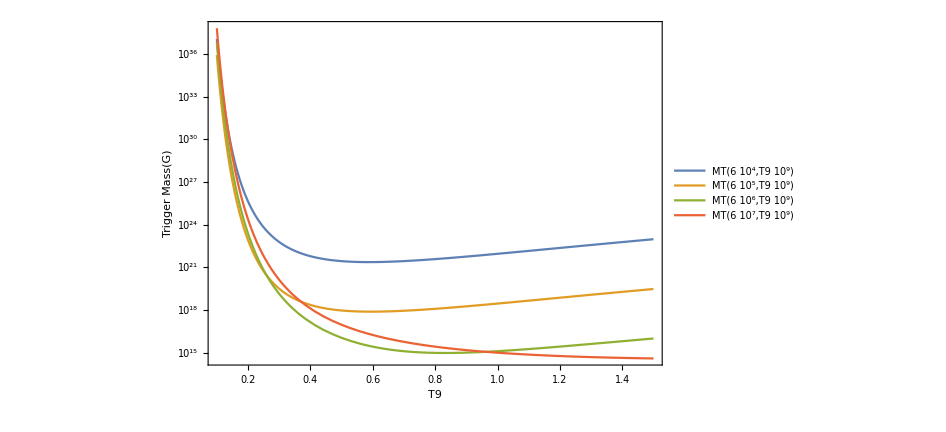

```mathematica
MT[6 10^5,10^9]
LogPlot[{MT[6 10^4,T9 10^9],MT[6 10^5,T9 10^9],MT[6 10^6,T9 10^9],MT[6 10^7,T9 10^9]},{T9,.1,1.5},ImageSize->700,Frame-> True,FrameStyle->Directive[FontSize-> 20],PlotLegends->"Expressions",FrameLabel->{"T9","Trigger Mass(G)"}]
```